## Chapter 8 : Machine Learning with the Wolfram Language

## 8.1 Gradient Descent Algorithm

### 8.1.1 Getting the Data

```mathematica
SeedRandom[888];
x=RandomReal[{0,1},50];
y=-1-x+0.6*RandomReal[{0,1},50];
```

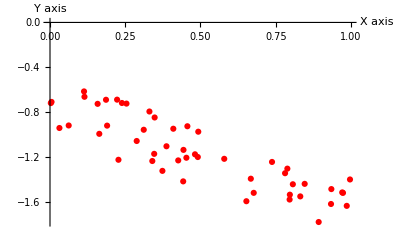

```mathematica
ListPlot[Transpose[{x,y}],AxesLabel->{"X axis","Y axis"},PlotStyle->Red]
```

### 8.1.2 Algorithm Implementation

```mathematica
itt=250;(*Number of iterations*)
α=0.0001;(*Learning rate*)
θ0=Range@@{0,itt};(* Array for values of Theta_0*)
θ1=Range@@{0,itt};(* Array for values of Theta_1*)
Table[{θ0⟦i+1⟧=θ0⟦i⟧-α/(Length@x)*Sum[(θ0⟦i⟧+θ1⟦i⟧* x⟦j⟧-y⟦j⟧),{j,1,Length@x}];
θ1⟦i+1⟧=θ1⟦i⟧-α/(Length@x)*Sum[( θ0⟦i⟧+θ1⟦i⟧*x⟦j⟧- y⟦j⟧)*x⟦j⟧,{j,1,Length@x}];},{i,1,itt}];
```

```mathematica
F[X_]:=θ0⟦Length@θ0⟧+θ1⟦Length@θ1⟧*X
```

```mathematica
F[X]
```

-0.0285289-0.0159621 X

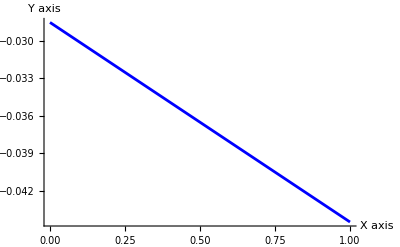

```mathematica
Show[{Plot[F[X],{X,0,1},PlotStyle->Blue,AxesLabel->{"X axis","Y axis"}],ListPlot[Transpose[{x,y}],PlotStyle->Red]}]
```

```mathematica
J[Theta0_,Theta1_]:=1/(2*Length[x])*Sum[ (Theta0+(Theta1*x[[i]])- y[[i]])^2,{i,1,Length@x}]
```

### 8.1.3 Multiple Alphas

```mathematica
α1=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

```mathematica
α2=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

```mathematica
α3=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

```mathematica
α4=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

```mathematica
α5=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

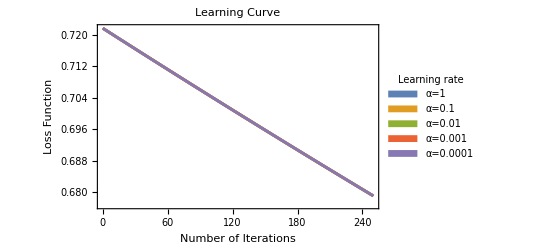

```mathematica
ListLinePlot[{α1,α2,α3,α4,α5},FrameLabel->{"Number of Iterations","Loss Function"},Frame->True,PlotLabel->"Learning Curve",PlotLegends->SwatchLegend[{Style["α=1",#],Style["α=0.1",#],Style["α=0.01",#],Style["α=0.001",#],Style["α=0.0001",#]},LegendLabel->Style["Learning rate",White],LegendFunction->(Framed[#,RoundingRadius->5,Background->Gray]&)]]&[White]
```

## 8.2 Linear Regression

### 8.2.1 Predict Function

### 8.2.2 Boston Dataset

```mathematica
bstn=ResourceData[ResourceObject["Sample Data: Boston Homes"]]
```

Dataset[<>]

```mathematica
ResourceData[ResourceObject["Sample Data: Boston Homes"],"ColumnDescriptions"]//TableForm
```

Per capita crime rate by town
Proportion of residential land zoned for lots over 25000 square feet
Proportion of non-retail business acres per town
Charles River dummy variable (1 if tract bounds river, 0 otherwise)
Nitrogen oxide concentration (parts per 10 million)
Average number of rooms per dwelling
Proportion of owner-occupied units built prior to 1940
Weighted mean of distances to five Boston employment centers
Index of accessibility to radial highways
Full-value property-tax rater per $10000
Pupil-teacher ratio by town
1000(Bk-0.63)^2 where Bk is the proportion of Black or African-American residents by town
Lower status of the population (percent)
Median value of owner-occupied homes in $1000s

### 8.2.3 Model Creation

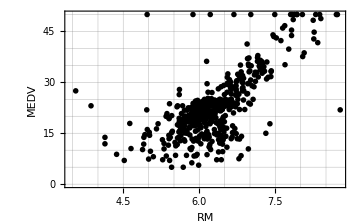

```mathematica
MEDVvsRM=Transpose[{Normal[bstn[All,"RM"]],Normal[bstn[All,"MEDV"]]}];
ListPlot[MEDVvsRM,PlotMarkers->"OpenMarkers",Frame->True,FrameLabel->{Style["RM",Red],Style["MEDV",Red]},GridLines->All,PlotStyle->Black,ImageSize->Medium]
```

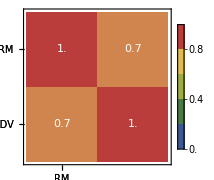

```mathematica
correLat=SetPrecision[Correlation[Transpose[{Normal[bstn[All,"RM"]],Normal[bstn[All,"MEDV"]]}]],2];
xTicks={{1,"RM"},{2,"MEDV"},{1,"RM"},{2,"MEDV"}};
yTicks={{1,"RM"},{2,"MEDV"},{1,"RM"},{2,"MEDV"}};
postionsValues={Text[#1,{0.5,1.5}],Text[#1,{1.5,0.5}],Text[#2,{1.5,1.5}],Text[#2,{0.5,0.5}]}&[correLat⟦1,1⟧,correLat⟦1,2⟧];
MatrixPlot[correLat,ColorFunction->"DarkRainbow",FrameTicks->{  xTicks,yTicks,xTicks,yTicks},Epilog->{White,postionsValues},PlotLegends->BarLegend[{"DarkRainbow",{0,1}},4],ImageSize->180]
```

```mathematica
newData=RandomSample[Thread[Normal[bstn[All,"RM"]]->Normal[bstn[All,"MEDV"]]]];
```

```mathematica
{training,test}={newData⟦;;354⟧,newData⟦355;;⟧};
```

```mathematica
pF=Predict[training,Method->"LinearRegression",TrainingProgressReporting->"Panel"]
```

PredictorFunction[…]

```mathematica
Information[pF]
```

Predictor information
Data type | Numerical
Standard deviation | 6.32 ± 0.5
Method | LinearRegression
Single evaluation time | 1.41 ms/example
Batch evaluation speed | 400. examples/ms
Loss | 3.27 ± 0.066
Model memory | 341. kB
Training examples used | 354 examples
Training time | 2.93 s
 |

### 8.2.4 Model Measurements

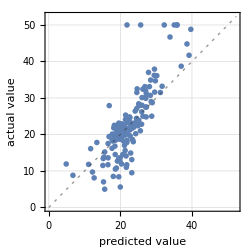
Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 152
Standard deviation | 6.1 ± 0.61
Standard deviation baseline | 9.7 ± 0.69
R-squared | 0.605 ± 0.098
Mean cross entropy | 3.24 ± 0.079
Single evaluation time | 1.45 ms/example
Batch evaluation speed | 2.27 examples/ms
-Graphics- |

```mathematica
pRM=PredictorMeasurements[pF,test]
```

```mathematica
pRM["Report"]
```

Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 152
Standard deviation | 6.1 ± 0.61
Standard deviation baseline | 9.7 ± 0.69
R-squared | 0.605 ± 0.098
Mean cross entropy | 3.24 ± 0.079
Single evaluation time | 1.45 ms/example
Batch evaluation speed | 2.27 examples/ms
-Graphics- |

```mathematica
Dataset[AssociationMap[pRM[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared"}]]
```

### 8.2.5 Model Assessment

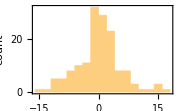
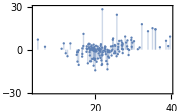
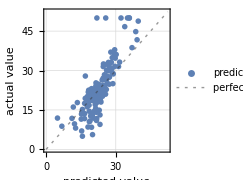

```mathematica
pRM[#]&/@{"ResidualHistogram","ResidualPlot","ComparisonPlot"}/. plot_Graphics:>Show[plot,ImageSize->Small]
```

```mathematica
pRM["Properties"]
```

{BatchEvaluationTime,BestPredictedExamples,ComparisonPlot,EvaluationTime,Examples,FractionVarianceUnexplained,GeometricMeanProbabilityDensity,ICEPlots,LeastCertainExamples,Likelihood,LogLikelihood,MeanCrossEntropy,MeanDeviation,MeanSquare,MostCertainExamples,Perplexity,PredictorFunction,ProbabilityDensities,ProbabilityDensityHistogram,Properties,RejectionRate,Report,ResidualHistogram,ResidualPlot,Residuals,RSquared,SHAPPlots,SHAPValues,StandardDeviation,StandardDeviationBaseline,TotalSquare,WorstPredictedExamples}

```mathematica
Information[pF,"MethodOption"]
```

Method→{LinearRegression,L1Regularization→0,L2Regularization→0.00001,OptimizationMethod→NormalEquation}

### 8.2.6 Retraining Model Hyperparameters

```mathematica
pF2=Predict[training,Method->{"LinearRegression","L1Regularization"-> 12,"L2Regularization"->100,"OptimizationMethod"-> Automatic},TrainingProgressReporting->None,PerformanceGoal->"Quality",RandomSeeding->10000,TargetDevice->"CPU"];
```

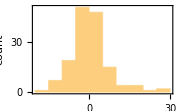
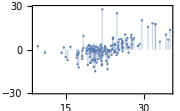
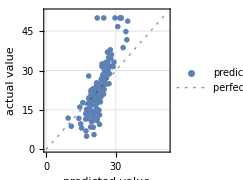

```mathematica
pRM2=PredictorMeasurements[pF2,test];
pRM2[#]&/@{"ResidualHistogram","ResidualPlot","ComparisonPlot"}/. plot_Graphics:>Show[plot,ImageSize->Small]
Dataset[AssociationMap[pRM2[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared"}]]
```

## 8.3 Logistic Regression

### 8.3.1 Titanic Dataset

```mathematica
titanic=Query[AssociationThread[Range[Length@#]->Range[Length@#]]][ExampleData[{"Dataset","Titanic"}]]&[ExampleData[{"Dataset","Titanic"}]]
```

Dataset[<>]

```mathematica
Dimensions@titanic
```

{1309,4}

```mathematica
Query[Count[_Missing],#]@titanic&/@{"class","age","sex","survived"}
```

{0,263,0,0}

```mathematica
Query[Select[#age==Missing[]&]][titanic];
Normal@Keys@%
```

{16,38,41,47,60,70,71,75,81,107,108,109,119,122,126,135,148,153,158,167,177,180,185,197,205,220,224,236,238,242,255,257,270,278,284,294,298,319,321,364,383,385,411,470,474,478,484,492,496,525,529,532,582,596,598,673,681,682,683,706,707,757,758,768,769,776,790,796,799,801,802,803,805,806,809,813,814,816,817,820,836,843,844,853,855,857,859,866,872,873,875,877,880,883,887,888,901,902,903,904,919,921,922,923,924,927,928,929,930,931,932,941,943,945,946,947,949,955,956,957,958,959,962,963,972,974,977,983,984,985,988,989,990,992,994,995,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1010,1013,1014,1015,1017,1019,1023,1024,1028,1029,1030,1031,1033,1034,1035,1036,1037,1038,1039,1040,1042,1043,1044,1045,1053,1054,1055,1056,1070,1071,1072,1073,1074,1075,1077,1078,1079,1081,1082,1086,1096,1110,1115,1116,1117,1122,1123,1124,1125,1129,1133,1136,1137,1138,1139,1150,1151,1152,1155,1156,1160,1163,1164,1165,1167,1168,1169,1171,1173,1174,1175,1176,1177,1178,1179,1180,1181,1185,1186,1187,1194,1195,1196,1198,1199,1200,1201,1203,1213,1214,1215,1216,1217,1220,1222,1242,1243,1244,1246,1247,1248,1250,1251,1254,1256,1263,1269,1283,1284,1285,1292,1293,1294,1298,1303,1304,1306}

```mathematica
titanic=DeleteMissing[titanic,1,1]
```

```mathematica
titanic[Key[16]]
```

Missing[KeyAbsent,Key[16]]

### 8.3.2 Data Exploration

```mathematica
Dataset@<|"Class"->Query[Counts,"class"]@titanic,"Sex"->Query[Counts,"sex"]@titanic,"Survival status"->Query[Counts,"survived"]@titanic|>
```

```mathematica
Row[{PieChart[{N@((#[[1]])/(Total@#)),N@((#[[2]])/(Total@#))}&[Counts[Query[All,"survived"][titanic]]], PlotLabel->Style["Percentage of survival",#3,#4], ChartLegends-> {"Survived", "Died"}, ImageSize->#1,ChartStyle->#2,LabelingFunction->(Placed[Row[{SetPrecision[100#,3],"%"}],"RadialCallout"]&)],
PieChart[{N@((#[[1]])/(Total@#)),N@((#[[2]])/(Total@#))}&[Counts[Query[All,"sex"][titanic]]], PlotLabel->Style["Percentage by sex",#3,#4], ChartLegends->{"Female", "Male"}, ImageSize->#1,ChartStyle->#2,LabelingFunction->(Placed[Row[{SetPrecision[100#,3],"%"}],"RadialCallout"]&)],
PieChart[{N@((#[[1]])/(Total@#)),N@((#[[2]])/(Total@#)),N@((#[[3]])/(Total@#))}&[Counts[Query[All,"class"][titanic]]], PlotLabel->Style["Percentage by class",#3,#4], ChartLegends->{"1st", "2nd","3rd"}, ImageSize->#1,ChartStyle->#2,LabelingFunction->(Placed[Row[{SetPrecision[100#,3],"%"}],"RadialCallout"]&)]},"----"]&[200,{ColorData[97,20],ColorData[97,13],ColorData[97,32]},Black,20]
```

---------Graphics--Graphics--Graphics-

```mathematica
BlockRandom[SeedRandom[8888];
RandomSample[titanic]];
Keys@Normal@Query[All][%];
{train,test}={%[[1;;837]],%[[838;;1046]]};
dataset=Query[<|"Train"->{Map[Key,train]},"Test"->{Map[Key,test]} |> ][titanic]
```

### 8.3.3 Classify Function

```mathematica
cF=Classify[Flatten[Values[Normal[Query["Train",All,All,{#class,#age,#sex}-> #survived&][dataset]]]],Method->{"LogisticRegression","L1Regularization"-> Automatic,"L2Regularization"-> Automatic,"OptimizationMethod"->"StochasticGradientDescent"},PerformanceGoal->"Quality",RandomSeeding->100000,TargetDevice->"CPU",TrainingProgressReporting->None]
```

ClassifierFunction[…]

```mathematica
Information[cF]
```

Classifier information
Data type | {Nominal,Numerical,Nominal}
Classes | ,,FalseTrue
Accuracy | (79.32.0) %
Method | LogisticRegression
Single evaluation time | 1.82 ms/example
Batch evaluation speed | 251. examples/ms
Loss | 0.513 ± 0.025
Model memory | 680. kB
Training examples used | 837 examples
Training time | 37.6 s
 |

```mathematica
Information[cF,"Properties"]
```

{AcceptanceThreshold,Accuracy,AnomalyDetector,BatchEvaluationSpeed,BatchEvaluationTime,Calibrated,Classes,ClassNumber,ClassPriors,EvaluationTime,ExampleNumber,FeatureExtractor,FeatureNames,FeatureNumber,FeatureTypes,FunctionMemory,FunctionProperties,IndeterminateThreshold,LearningCurve,MaxTrainingMemory,MeanCrossEntropy,Method,MethodDescription,MethodOption,MethodParameters,MissingSynthesizer,PerformanceGoal,Properties,TrainingClassPriors,TrainingTime,UtilityFunction}

```mathematica
cF[{"3rd",23,"male"},{"Probability"-> False,"TopProbabilities"-> 2}]
```

{0.676982,{False→0.676982,True→0.323018}}

```mathematica
Dataset@
AssociationMap[cF[{"3rd",23,"male"},#]
&,{"Decision","Distribution","ExpectedUtilities","LogProbabilities","Probabilities","TopProbabilities"}]
```

### 8.3.4 Testing the Model

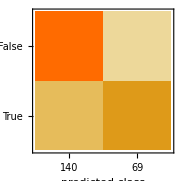
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 209
Accuracy | (73.73.1) %
Accuracy baseline | (60.83.4) %
Geometric mean of probabilities | 0.563 ± 0.012
Mean cross entropy | 0.575 ± 0.021
Single evaluation time | 2.35 ms/example
Batch evaluation speed | 37.5 examples/ms
-Graphics- |

```mathematica
cM=ClassifierMeasurements[cF,Flatten[Values[Normal[Query["Test",All,All,{#class,#age,#sex}-> #survived&][dataset]]]],ComputeUncertainty->True,RandomSeeding->8888]
```

```mathematica
cM["Report"];
```

```mathematica
cM["ConfusionMatrixPlot"]
```

-Graphics-

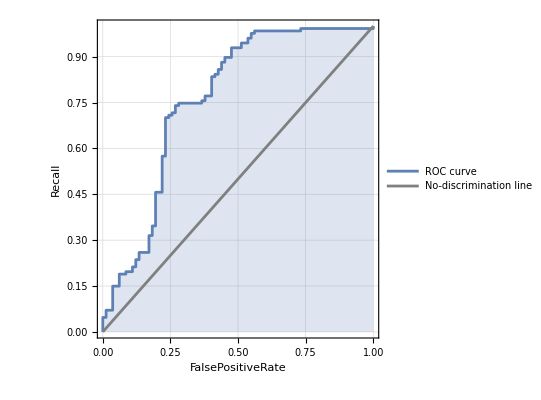
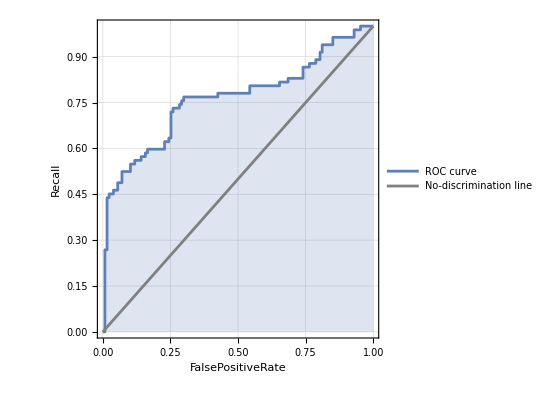
{<|False→-Graphics-,True→-Graphics-|>,}

```mathematica
{cM["ROCCurve"],Dataset@<|{"AUC"->cM["AreaUnderROCCurve"]},{"MCC"->cM["MatthewsCorrelationCoefficient"]}|>}
```

```mathematica
cM[{"LeastCertainExamples","ClassMeanCrossEntropy"}]
```

{{{1st,4,male}→True,{1st,19,male}→False,{1st,22,male}→False,{1st,24,male}→False,{1st,25,male}→False,{1st,27,male}→False,{1st,29,male}→False,{1st,30,male}→False,{1st,33,male}→False,{1st,35,male}→True},<|False→0.552204,True→0.611137|>}

```mathematica
cM[#]&/@{"FalseDiscoveryRate","FalseNegativeRate","FalsePositiveRate"}
```

{<|False→0.242857,True→0.304348|>,<|False→0.165354,True→0.414634|>,<|False→0.414634,True→0.165354|>}

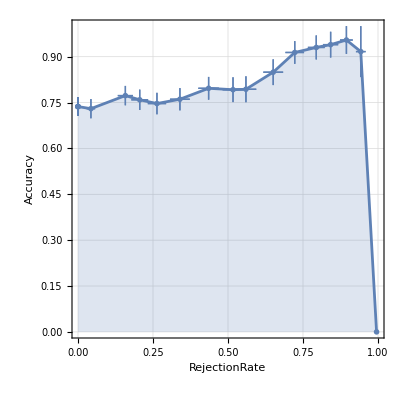
0.736842
<|False→0.834646,True→0.585366|>
<|False→0.794007,True→0.635762|>
<|False→0.757143,True→0.695652|>
-Graphics-

```mathematica
cM[{"Accuracy","Recall","F1Score","Precision","AccuracyRejectionPlot"}]//TableForm
```

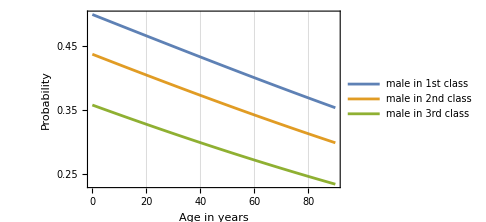
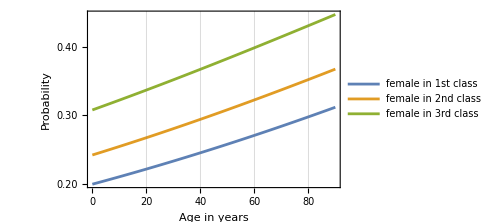
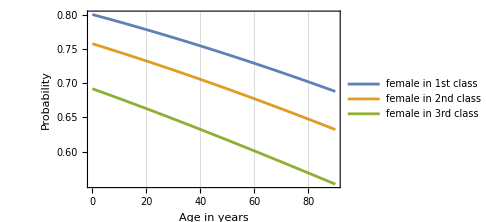
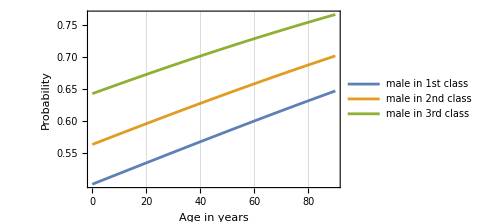
True class | False class
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
plotClass[class1_,class2_,class3_,gender_,prob_,frame_,ticks_,imgSize_]:=Plot[{cF[{class1,age,gender},"Probability"->prob],cF[{class2,age,gender},"Probability"->prob],cF[{class3,age,gender},"Probability"->prob]},{age,0,90},PlotLegends->{gender<>" in 1st class",gender<>" in 2nd class",gender<>" in 3rd class"},FrameLabel->{Style["Age in years",Bold,15],Style["Probability",Bold,15]},Frame->frame,FrameTicks->ticks,GridLines->{{20,40,60,80}},ImageSize->imgSize]

truPlot={plotClass["1st","2nd","3rd","male",True,True,All,Medium],plotClass["1st","2nd","3rd","female",True,True,All,Medium]};
falsePlot={plotClass["1st","2nd","3rd","male",False,True,All,Medium],plotClass["1st","2nd","3rd","female",False,True,All,Medium]};
headings={Style["True class",Black,20,FontFamily->"Arial Rounded MT"],Style["False class",Black,20,FontFamily->"Arial Rounded MT"]};

Grid[{{headings[[1]],headings[[2]]},{truPlot[[1]],falsePlot[[2]]},{truPlot[[2]],falsePlot[[1]]}},Alignment->{{Center,Center},{None,None}},Dividers->{False,1}]
```

## 8.4 Data Clustering

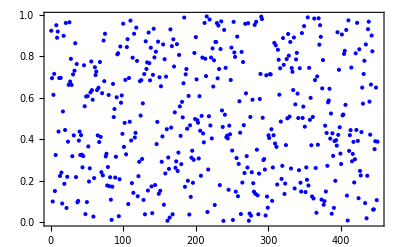

```mathematica
BlockRandom[
SeedRandom[321];
rndPts=Table[{i,RandomReal[{0,1}]},{i,1,450}];]
ListPlot[rndPts,PlotRange->All,PlotStyle->Directive[Thick,Blue],Frame->True,FrameTicks->All]
```

### 8.4.1 Clusters Identification

```mathematica
clusters=FindClusters[rndPts,PerformanceGoal->"Speed",Method->Automatic,DistanceFunction->Automatic,RandomSeeding->1234];
Short[clusters,1]
```

{{{1,0.924416},{8,0.951038},{9,0.89058},{10,0.920375},«157»,{437,0.931815},{438,0.968112},{442,0.901215},{443,0.824999}},«1»,{«1»,«142»}}

```mathematica
Length[clusters]
```

3

```mathematica
Map[Dimensions,clusters,1]
```

{{165,2},{142,2},{143,2}}

```mathematica
ListPlot[clusters,PlotStyle->{Red,Blue,Green},PlotLegends->Automatic,Frame->True,FrameTicks->All,PlotLabel->Style["Cluster Plot",Italic,20,Black],Prolog->{LightYellow,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}]
```

-Graphics-

### 8.4.2 Choosing a Distance Function

```mathematica
{cluster1Centroid,cluster2Centroid,cluster3Centroid}={N@Mean@clusters⟦1,All⟧,N@Mean@clusters⟦2,All⟧,N@Mean@clusters⟦3,All⟧}
```

{{224.806,0.810328},{347.514,0.31097},{105.14,0.331805}}

```mathematica
clusterPlot=ListPlot[clusters,PlotStyle->{Red,Blue,Green},PlotLegends->{"Cluster 1","Cluster 2","Cluster 3"}];
centroidPlot=ListPlot[{cluster1Centroid,cluster2Centroid,cluster3Centroid},PlotStyle->Black];
Show[{clusterPlot,centroidPlot},Prolog->{LightYellow,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Frame-> True,FrameTicks-> All,PlotLabel->Style["Cluster Plot",Italic,20,Black]]
```

-Graphics-

```mathematica
Show[{clusterPlot,centroidPlot},Prolog->{LightYellow,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Frame-> True,FrameTicks-> All,Epilog->{Opacity[0.2],PointSize[0.1],Point[cluster1Centroid],Point[cluster2Centroid],Point[cluster3Centroid]}]
```

-Graphics-

### 8.4.3 Identifying Classes

```mathematica
classes=ClusteringComponents[clusters,3,2,Method->Automatic,DistanceFunction->Automatic,RandomSeeding-> 1234,PerformanceGoal->"Speed"]
```

{{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,2,3,2,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,2,2,1,1,2,1,1,1,2,1,1,1,1,2,2,2,1,1,2,2,2,1,1,1,2,2,2,1,1,1,1,2,2,2,1,2,1,1,1,2,1,2,1,1,2,1,2,2,2,2,2,2,2,1,2,2,1,2,1,2,2,2,2,2,2,2,2,2,1,1,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,1,1,2,2,2,2,1,1,2,2,2,1,2},{3,1,3,3,1,1,3,3,1,3,1,1,3,1,3,1,1,3,3,3,3,1,3,1,1,1,3,3,1,3,1,1,1,3,1,3,1,3,1,1,1,3,3,3,1,1,3,3,3,1,3,1,3,1,1,1,1,1,3,1,1,1,1,1,3,3,1,1,3,1,1,3,3,3,1,3,1,1,3,1,1,1,1,1,1,1,1,3,1,3,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
Flatten[classes]//Counts
```

<|3→135,1→178,2→137|>

### 8.4.4 K-Means Clustering

```mathematica
ExampleData[{"Statistics","FisherIris"},"ColumnDescriptions"]
```

{Sepal length in cm.,Sepal width in cm.,Petal length in cm.,Petal width in cm.,Species of iris}

```mathematica
iris=ExampleData[{"Statistics","FisherIris"}];
Short[iris,6]
```

{{5.1,3.5,1.4,0.2,setosa},{4.9,3.,1.4,0.2,setosa},{4.7,3.2,1.3,0.2,setosa},{4.6,3.1,1.5,0.2,setosa},{5.,3.6,1.4,0.2,setosa},{5.4,3.9,1.7,0.4,setosa},{4.6,3.4,1.4,0.3,setosa},{5.,3.4,1.5,0.2,setosa},{4.4,2.9,1.4,0.2,setosa},{4.9,3.1,1.5,0.1,setosa},{5.4,3.7,1.5,0.2,setosa},{4.8,3.4,1.6,0.2,setosa},{4.8,3.,1.4,0.1,setosa},{4.3,3.,1.1,0.1,setosa},{5.8,4.,1.2,0.2,setosa},{5.7,4.4,1.5,0.4,setosa},«119»,{7.7,3.,6.1,2.3,virginica},{6.3,3.4,5.6,2.4,virginica},{6.4,3.1,5.5,1.8,virginica},{6.,3.,4.8,1.8,virginica},{6.9,3.1,5.4,2.1,virginica},{6.7,3.1,5.6,2.4,virginica},{6.9,3.1,5.1,2.3,virginica},{5.8,2.7,5.1,1.9,virginica},{6.8,3.2,5.9,2.3,virginica},{6.7,3.3,5.7,2.5,virginica},{6.7,3.,5.2,2.3,virginica},{6.3,2.5,5.,1.9,virginica},{6.5,3.,5.2,2.,virginica},{6.2,3.4,5.4,2.3,virginica},{5.9,3.,5.1,1.8,virginica}}

### 8.4.5 Dimensionality Reduction

```mathematica
sT=Standardize[iris[[All,{1,2,3,4}]]];(*Showing only the first 4 terms*)
%[[1;;4]]//TableForm
```

-0.897674 | 1.0156 | -1.33575 | -1.31105
-1.1392 | -0.131539 | -1.33575 | -1.31105
-1.38073 | 0.327318 | -1.3924 | -1.31105
-1.50149 | 0.0978893 | -1.2791 | -1.31105

```mathematica
dR=DimensionReduction[sT,2,Method->"Linear"]
```

DimensionReducerFunction[…]

```mathematica
pCA=dR[sT,"ReducedVectors"];
TableForm[%[[1;;5]],TableHeadings->{None, {"First principal component","Second Principal component"}},TableAlignments->Center]
```

First principal component | Second Principal component
2.2647 | -0.480027
2.08096 | 0.674134
2.36423 | 0.341908
2.29938 | 0.597395
2.38984 | -0.646835

```mathematica
(Variance@pCA⟦All,All⟧)/(Total@Variance@pCA⟦All,All⟧)//TableForm[#,TableHeadings->{{"First PC variation","Second PC variation"}, None}]&
```

First PC variation | 0.761507
Second PC variation | 0.238493

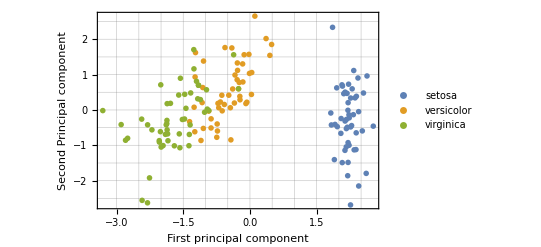

```mathematica
labels={Style["First principal component",Black,Bold],Style["Second Principal component",Black,Bold]};
ListPlot[{pCA⟦1;;50⟧,pCA⟦51;;100⟧,pCA⟦100;;150⟧},PlotLegends->Placed[{Placeholder["setosa"],Placeholder["versicolor"],Placeholder["virginica"]},Right],PlotMarkers->"OpenMarkers",GridLines->All,Frame->True,Axes->False,FrameTicks->All,FrameLabel->labels]
```

### 8.4.6 Applying K-Means

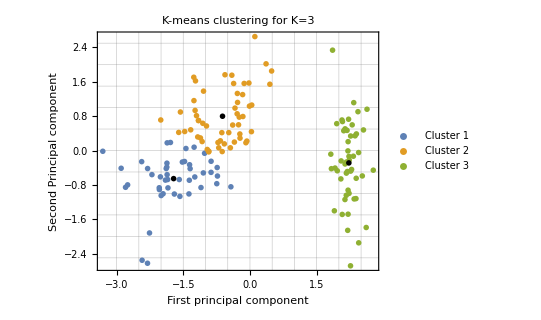

```mathematica
clstr=FindClusters[pCA,3,Method->"KMeans",DistanceFunction->SquaredEuclideanDistance,RandomSeeding->8888];
ListPlot[clstr,PlotRange->All,Frame->True,AspectRatio->0.8,Axes->False,PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3]},PlotLabel->Style["K-means clustering for K=3",FontFamily->"Times",Black,20,Italic],FrameTicks->All,PlotLegends->Placed[{Placeholder[Style["Cluster 1",Bold,Black,10]],Placeholder[Style["Cluster 2",Bold,Black,10]],Placeholder[Style["Cluster 3",Bold,Black,10]]},Right],PlotMarkers-> "OpenMarkers",FrameLabel->labels,GridLines->All,Epilog->{Opacity[1],PointSize[0.01],Point[Mean@clstr⟦1,All⟧],Point[Mean@clstr⟦2,All⟧],Point[Mean@clstr⟦3,All⟧]}]
```

### 8.4.7 Chaining the Distance Function

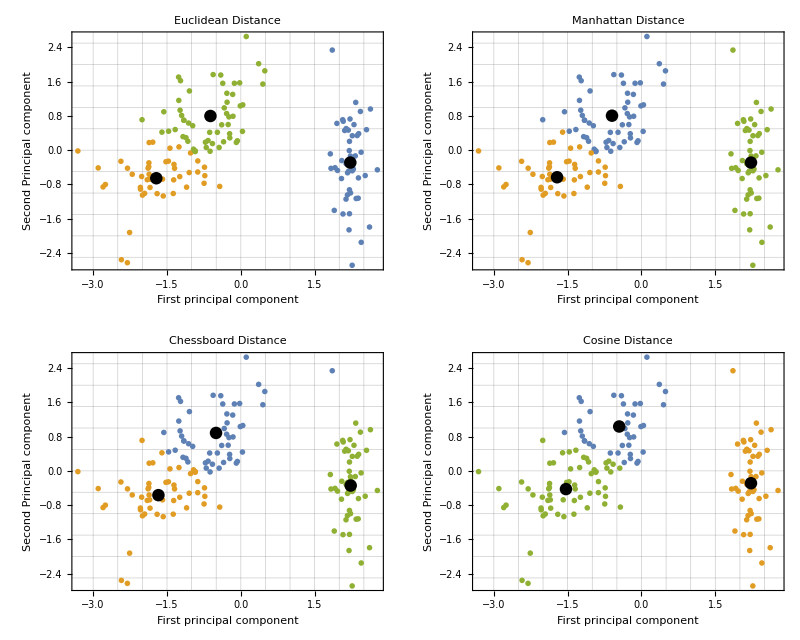
-Graphics-K-means clustering for K=3

```mathematica
clusteringPlot[distanceName_,distanceFunction_]:=Module[{clusters,pltTitles,points},clusters=FindClusters[pCA,3,PerformanceGoal->"Quality",Method->"KMeans",DistanceFunction->distanceFunction,RandomSeeding->8888];
points=Point[Mean[#]]&/@clusters;
pltTitles=distanceName;
ListPlot[clusters,Frame->True,AspectRatio->0.8,PlotMarkers->"OpenMarkers",PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3]},GridLines->All,PlotRange->Automatic,ImageSize->300,FrameLabel->labels,Axes->False,FrameTicks->All,Epilog->{Opacity@1,PointSize@0.03,points},PlotLabel->Style[pltTitles,Black]]]

eDplt=clusteringPlot["Euclidean Distance",EuclideanDistance];
mhDplt=clusteringPlot["Manhattan Distance",ManhattanDistance];
chDplt=clusteringPlot["Chessboard Distance",ChessboardDistance];
cosDplt=clusteringPlot["Cosine Distance",CosineDistance];

legendsText={Placeholder[Style["Cluster 1",Bold,Black,10]],Placeholder[Style["Cluster 2",Bold,Black,10]],Placeholder[Style["Cluster 3",Bold,Black,10]]};
Labeled[Legended[GraphicsGrid[{{eDplt,mhDplt},{chDplt,cosDplt}},Frame->All,Background->White,Spacings->1],PointLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3]},legendsText,LegendMarkers->"OpenMarkers"]],Style["K-means clustering for K=3",FontFamily->"Times",Black,20,Italic],Top]
```

### 8.4.8 Different K’s

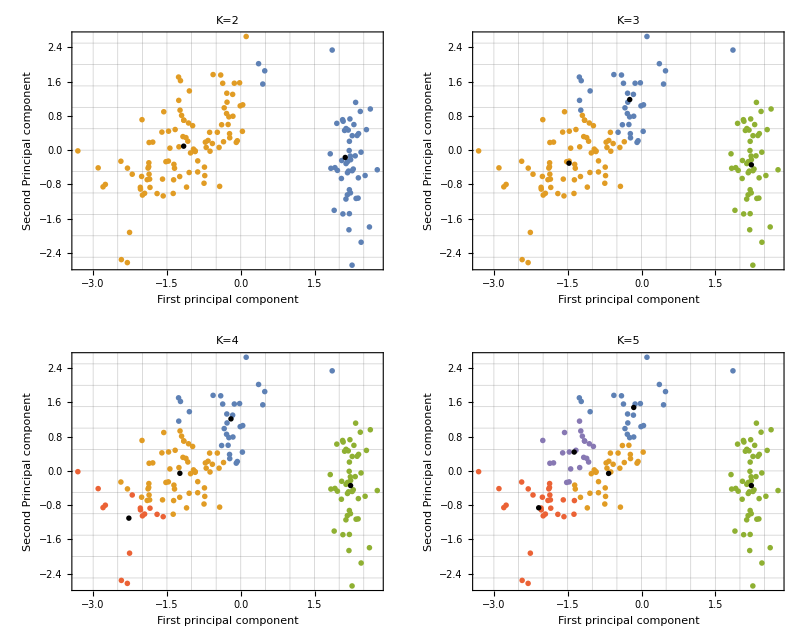
-Graphics-K-means clustering for K=2,3,4,5

```mathematica
findKClusters[k_,PCA_]:=FindClusters[PCA,k,PerformanceGoal->"Speed",Method->"KMeans",DistanceFunction->SquaredEuclideanDistance,RandomSeeding->8888];

plotKClusters[k_,clusters_]:=ListPlot[clusters,Frame->True,AspectRatio->0.8,PlotMarkers->"OpenMarkers",PlotStyle->ColorData[97,"ColorList"][[;;k]],GridLines->All,PlotRange->Automatic,ImageSize->260,FrameLabel->labels,Axes->False,FrameTicks->All,Epilog->{Opacity@1,PointSize@0.015,Point[Mean/@clusters]},PlotLabel->Style["K="<>ToString[k],Black]];

kValues={2,3,4,5};
kClusters=findKClusters[#,pCA]&/@kValues;
kPlots=plotKClusters[#,kClusters[[#2]]]&@@@Transpose[{kValues,Range@Length@kValues}];

legendsText2={Placeholder[Style["Cluster "<>ToString[#],Bold,Black,10]]}&/@Range@5;

Labeled[Legended[GraphicsGrid[Partition[kPlots,2],Frame->All,Background->White,Spacings->1],PointLegend[ColorData[97,"ColorList"][[;;5]],legendsText2,LegendMarkers->"OpenMarkers"]],Style["K-means clustering for K=2,3,4,5",FontFamily->"Times",Black,20,Italic],Top]
```

```mathematica
ClusteringComponents[clstr,3,2,Method->"KMeans",DistanceFunction->SquaredEuclideanDistance,RandomSeeding->8888]
Counts[Flatten[%]]
```

{{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

<|3→45,2→55,1→50|>

### 8.4.9 Cluster Classify

```mathematica
BlockRandom[
SeedRandom[88888];
RandomSample[iris⟦All,{1,2}⟧];]
trainingSet=%⟦1;;75⟧;
testSet=%%⟦76;;150⟧;
```

```mathematica
cC=ClusterClassify[trainingSet,3,Method->"KMeans",DistanceFunction->Automatic,PerformanceGoal->"Speed",RandomSeeding->8888 ]
```

ClassifierFunction[…]

```mathematica
Information[cC]
```

Classifier information
Data type | NumericalVector (××2)
Classes | ,,123
Method | KMeans
Single evaluation time | 1.65 ms/example
Batch evaluation speed | 235. examples/ms
Model memory | 73.9 kB
Training examples used | 75 examples
Training time | 1.46 ms

```mathematica
Information[cC,"Properties"]
```

{AcceptanceThreshold,AnomalyDetector,BatchEvaluationSpeed,BatchEvaluationTime,Calibrated,Classes,ClassNumber,ClassPriors,DistanceFunction,EvaluationTime,ExampleNumber,FeatureExtractor,FeatureNames,FeatureNumber,FeatureTypes,FunctionMemory,FunctionProperties,IndeterminateThreshold,LearningCurve,MaxTrainingMemory,Method,MethodDescription,MethodOption,MethodParameters,MissingSynthesizer,PerformanceGoal,Properties,TrainingClassPriors,TrainingTime,UtilityFunction}

```mathematica
Information[cC,#]&/@{"Classes","ClassNumber","DistanceFunction","FeatureNames","TrainingClassPriors"}
```

{{1,2,3},3,EuclideanDistance,{f1},<|1→0.333333,2→0.293333,3→0.373333|>}

```mathematica
Dataset[AssociationMap[cC[{1,2},#]&,{"Decision","Distribution","ExpectedUtilities","LogProbabilities","Probabilities","TopProbabilities"}]]
```

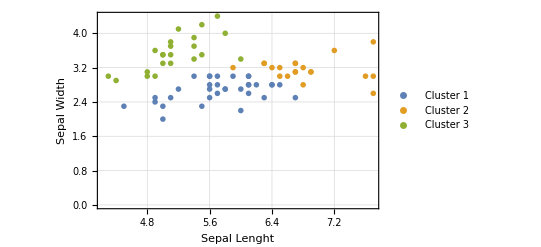

```mathematica
ListPlot[Pick[testSet,cC[testSet],#]&/@{1,2,3},PlotMarkers->"OpenMarkers",GridLines->Automatic,PlotLegends->{Placeholder[Style["Cluster 1",Bold,Black,10]],Placeholder[Style["Cluster 2",Bold,Black,10]],Placeholder[Style["Cluster 3",Bold,Black,10]]},Frame->True,FrameTicks->All,FrameLabel->{"Sepal Lenght","Sepal Width"}]
```

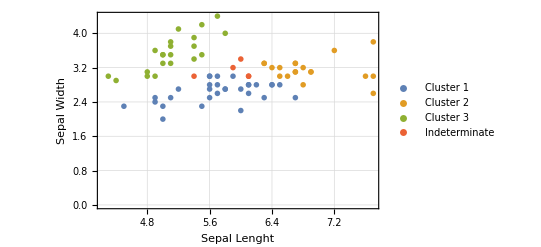

```mathematica
ListPlot[Pick[testSet,cC[testSet,IndeterminateThreshold-> 0.6],#]&/@{1,2,3,Indeterminate},PlotMarkers-> "OpenMarkers",PlotLegends->{Placeholder[Style["Cluster 1",Bold,Black,10]],Placeholder[Style["Cluster 2",Bold,Black,10]],Placeholder[Style["Cluster 3",Bold,Black,10]],Placeholder[Style["Indeterminate",Bold,Black,10]]},Frame->True,FrameTicks->All,FrameLabel->{"Sepal Lenght","Sepal Width"},GridLines->Automatic]
```